# 5440 Prelim 1 Problem 2: POP

```mathematica
Clear["Global`*"]
```

## Define Functions

```mathematica
f6p=0.1;
atp=2.3;
pfk=0.00012;
Kf6p=0.11;
Katp=0.42;
kCat=0.4;
```

```mathematica
r1=kCat*pfk(f6p/(Kf6p+f6p))(atp/(Katp+atp));
```

```mathematica
r1
```

0.0000193277

```mathematica
v1=(w1+w2(AMP/Kamp)/(1+AMP/Kamp))/(1+w1+w2(AMP/Kamp)/(1+AMP/Kamp));
```

```mathematica
rate[w1_,w2_,AMP_,Kamp_]=v1*r1;
```

```mathematica
data={{0,3.003},{0.055,6.302},{0.093,29.761},{.181,52.002},{.405,60.306},{.99,68.653}};
```

```mathematica
Do[
data[[i,2]]=data[[i,2]]*10^-3/60/60;,
{i,6}
]
```

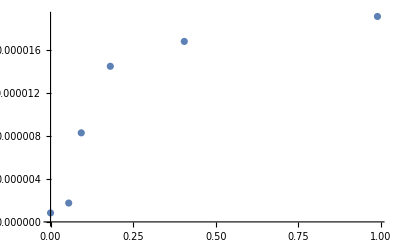

```mathematica
datapoints=ListPlot[data]
```

```mathematica
nlm=NonlinearModelFit[data,rate[w1,w2,AMP,Kamp],{w1,w2,Kamp},AMP]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[(0.0000193277 (-0.0344631+(«18» «3»)/(1+«1»)))/(0.965537+(8.92485 AMP)/(1+«23» AMP))]

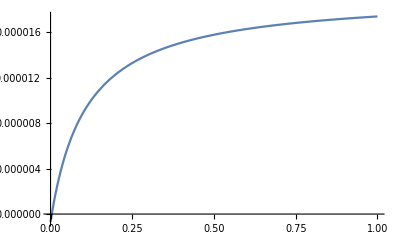

```mathematica
fitcurve=Plot[nlm[amp],{amp,0,1}]
```

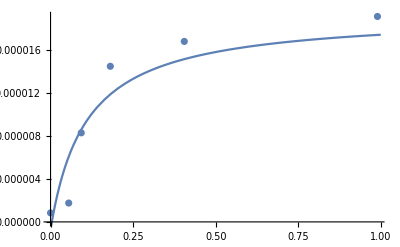

```mathematica
Show[datapoints,fitcurve]
```

```mathematica
Normal[nlm]
```

(0.0000193277 (-0.0344631+(8.92485 AMP)/(1+2.49939×10^-14 AMP)))/(0.965537+(8.92485 AMP)/(1+2.49939×10^-14 AMP))